```mathematica
(* Ricker wavelet with the dominant frequency of 40 Hz. The fourth derivative of the wavelt is used as the source wavelet in the scalar anisotropic wave equation. *)
```

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/media/sursf/4E1AEA7B1AEA6007/discB/desk/Submitted Papers/A-Geophysics/A-codes/A8-VA_ANI_WEQ20190817/vawe

```mathematica
WaveletSource[fm_,t_]:=Module[{ft,t0,ft0},
t0=1/fm;

ft=(1-2 Pi^2 fm^2 (t-t0)^2) Exp[-Pi^2 fm^2 (t-t0)^2];

Return[ft];
];
```

```mathematica
fc=40;
```

```mathematica
n=4000;
```

```mathematica
dt=0.0005;
```

```mathematica
maxt=(n-1)*dt;
```

```mathematica
omegamax=Pi/dt
```

6283.19

```mathematica
tdata=Table[WaveletSource[fc,t],{t,0,maxt,dt}];
```

```mathematica
Length[tdata]
```

4000

```mathematica
tValues=Table[dt (i-1),{i,1,n}];
```

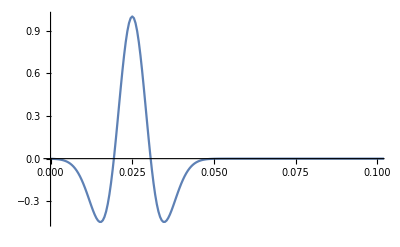

```mathematica
ListLinePlot[Table[{tValues[[i]],tdata[[i]]},{i,1,n}],PlotRange->{{0,4/fc},Full}]
```

```mathematica
Length[tdata]
```

4000

```mathematica
(* ----------------- output plots --------------------------- *)
```

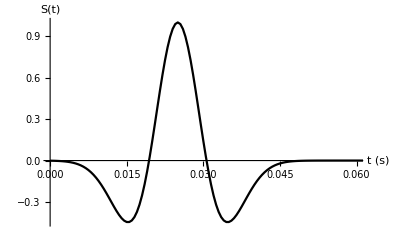

```mathematica
fig1=ListLinePlot[Table[{tValues[[i]],tdata[[i]]},{i,1,n}],PlotRange->{{0.0,0.06},Full},PlotStyle->Black,LabelStyle->{Directive[Black,20],Directive[Black,20]},AxesLabel->{Style["t (s)",FontSize->20],Style["S(t)",FontSize->20]},ImageSize->400,AxesStyle->{Directive[Black,20],Directive[Black,20]}]
```

```mathematica
Export["figure1.pdf",%]
```

figure1.pdf